```mathematica
Table[If[GCD[a,n]>1,Subscript[1, n],0],{a,35},{n,a-1}]//TableForm
```

|  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 1_2 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 0 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 1_2 | 1_3 | 1_4 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 0 | 0 | 0 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 1_2 | 0 | 1_4 | 0 | 1_6 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 0 | 1_3 | 0 | 0 | 1_6 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 1_2 | 0 | 1_4 | 1_5 | 1_6 | 0 | 1_8 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 1_2 | 1_3 | 1_4 | 0 | 1_6 | 0 | 1_8 | 1_9 | 1_10 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 1_2 | 0 | 1_4 | 0 | 1_6 | 1_7 | 1_8 | 0 | 1_10 | 0 | 1_12 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 0 | 1_3 | 0 | 1_5 | 1_6 | 0 | 0 | 1_9 | 1_10 | 0 | 1_12 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 1_2 | 0 | 1_4 | 0 | 1_6 | 0 | 1_8 | 0 | 1_10 | 0 | 1_12 | 0 | 1_14 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 1_2 | 1_3 | 1_4 | 0 | 1_6 | 0 | 1_8 | 1_9 | 1_10 | 0 | 1_12 | 0 | 1_14 | 1_15 | 1_16 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 1_2 | 0 | 1_4 | 1_5 | 1_6 | 0 | 1_8 | 0 | 1_10 | 0 | 1_12 | 0 | 1_14 | 1_15 | 1_16 | 0 | 1_18 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 0 | 1_3 | 0 | 0 | 1_6 | 1_7 | 0 | 1_9 | 0 | 0 | 1_12 | 0 | 1_14 | 1_15 | 0 | 0 | 1_18 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 1_2 | 0 | 1_4 | 0 | 1_6 | 0 | 1_8 | 0 | 1_10 | 1_11 | 1_12 | 0 | 1_14 | 0 | 1_16 | 0 | 1_18 | 0 | 1_20 | 0 |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  | 
0 | 1_2 | 1_3 | 1_4 | 0 | 1_6 | 0 | 1_8 | 1_9 | 1_10 | 0 | 1_12 | 0 | 1_14 | 1_15 | 1_16 | 0 | 1_18 | 0 | 1_20 | 1_21 | 1_22 | 0 |  |  |  |  |  |  |  |  |  |  | 
0 | 0 | 0 | 0 | 1_5 | 0 | 0 | 0 | 0 | 1_10 | 0 | 0 | 0 | 0 | 1_15 | 0 | 0 | 0 | 0 | 1_20 | 0 | 0 | 0 | 0 |  |  |  |  |  |  |  |  |  | 
0 | 1_2 | 0 | 1_4 | 0 | 1_6 | 0 | 1_8 | 0 | 1_10 | 0 | 1_12 | 1_13 | 1_14 | 0 | 1_16 | 0 | 1_18 | 0 | 1_20 | 0 | 1_22 | 0 | 1_24 | 0 |  |  |  |  |  |  |  |  | 
0 | 0 | 1_3 | 0 | 0 | 1_6 | 0 | 0 | 1_9 | 0 | 0 | 1_12 | 0 | 0 | 1_15 | 0 | 0 | 1_18 | 0 | 0 | 1_21 | 0 | 0 | 1_24 | 0 | 0 |  |  |  |  |  |  |  | 
0 | 1_2 | 0 | 1_4 | 0 | 1_6 | 1_7 | 1_8 | 0 | 1_10 | 0 | 1_12 | 0 | 1_14 | 0 | 1_16 | 0 | 1_18 | 0 | 1_20 | 1_21 | 1_22 | 0 | 1_24 | 0 | 1_26 | 0 |  |  |  |  |  |  | 
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 |  |  |  |  |  | 
0 | 1_2 | 1_3 | 1_4 | 1_5 | 1_6 | 0 | 1_8 | 1_9 | 1_10 | 0 | 1_12 | 0 | 1_14 | 1_15 | 1_16 | 0 | 1_18 | 0 | 1_20 | 1_21 | 1_22 | 0 | 1_24 | 1_25 | 1_26 | 1_27 | 1_28 | 0 |  |  |  |  | 
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 |  |  |  | 
0 | 1_2 | 0 | 1_4 | 0 | 1_6 | 0 | 1_8 | 0 | 1_10 | 0 | 1_12 | 0 | 1_14 | 0 | 1_16 | 0 | 1_18 | 0 | 1_20 | 0 | 1_22 | 0 | 1_24 | 0 | 1_26 | 0 | 1_28 | 0 | 1_30 | 0 |  |  | 
0 | 0 | 1_3 | 0 | 0 | 1_6 | 0 | 0 | 1_9 | 0 | 1_11 | 1_12 | 0 | 0 | 1_15 | 0 | 0 | 1_18 | 0 | 0 | 1_21 | 1_22 | 0 | 1_24 | 0 | 0 | 1_27 | 0 | 0 | 1_30 | 0 | 0 |  | 
0 | 1_2 | 0 | 1_4 | 0 | 1_6 | 0 | 1_8 | 0 | 1_10 | 0 | 1_12 | 0 | 1_14 | 0 | 1_16 | 1_17 | 1_18 | 0 | 1_20 | 0 | 1_22 | 0 | 1_24 | 0 | 1_26 | 0 | 1_28 | 0 | 1_30 | 0 | 1_32 | 0 | 
0 | 0 | 0 | 0 | 1_5 | 0 | 1_7 | 0 | 0 | 1_10 | 0 | 0 | 0 | 1_14 | 1_15 | 0 | 0 | 0 | 0 | 1_20 | 1_21 | 0 | 0 | 0 | 1_25 | 0 | 0 | 1_28 | 0 | 1_30 | 0 | 0 | 0 | 0

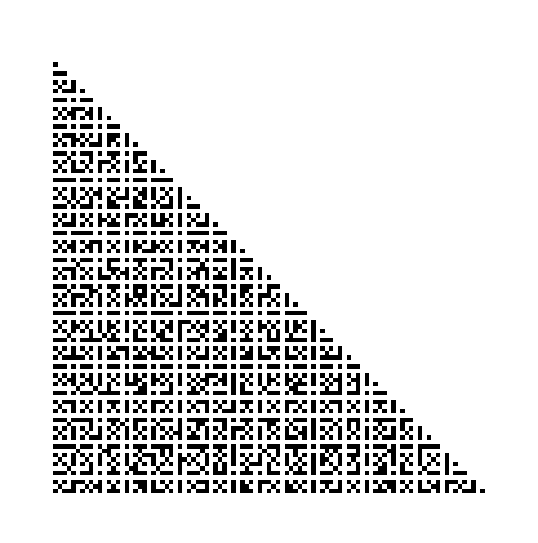

```mathematica
Table[If[GCD[a,n]>1,1,0],{a,100},{n,a-1}]//ArrayPlot
```

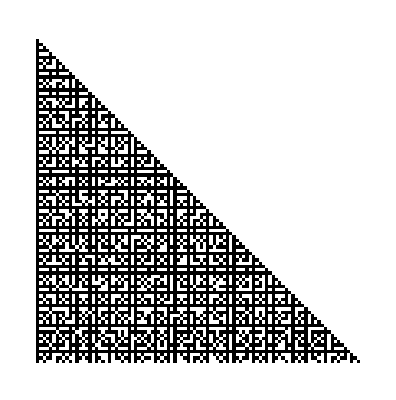

```mathematica
Table[If[GCD[a,n]>1,0,1],{a,100},{n,a-1}]//ArrayPlot
```